Simplify with 2 prey

```mathematica
VarTablefunc[{prey1_,prey2_,diff_}] := (
VarZTable=Table[
nprey = 12;
(*EX = {-15.5,-17.5,-15.6,-15.5,-14.3,-15.4,-16.0,-17.0,-15.8,-13.3,-17.5,-16.2};*)
EX = {-15.5,-17.5,-15.6,-15.5,-14.3,-15.4,-15.66+diff,-15.66+diff,-15.8,-13.3,-17.5,-16.2};
VarX = {1.00,0.81,0.49,0.81,0.81,0.81,0.25,1.21,0.64,1.21,1.96,1.00};
Dparam =Table[1,{nprey}];
Dparam[[prey1]] = a;
Dparam[[prey2]] = a;
a0 = Total[Dparam];
Ep = N[Dparam/a0];
Varp = N[Table[(Dparam[[i]]*(a0-Dparam[[i]]))/(a0^2*(a0+1)),{i,1,nprey}]];
Covp = N[Table[(-Dparam[[i]]*Dparam[[j]])/(a0^2*(a0+1))Boole[i ≠ j],{i,1,nprey},{j,1,nprey}]];
VarZ = N[Sum[Varp[[i]]*VarX[[i]] + Ep[[i]]^2*VarX[[i]] + EX[[i]]^2*Varp[[i]] + Sum[Covp[[i]][[j]]*EX[[i]]*EX[[j]]Boole[i ≠ j],{j,1,nprey}],{i,1,nprey}]];
propi = a/a0;
{propi,VarZ},
{a,1,1000,1}];
VarXTable = Table[{VarZTable[[i]][[1]],(λ*VarZTable[[i]][[2]])/2},{λ,0,1,0.1},{i,1,Length[VarZTable]}];
Return[{VarZTable,VarXTable}];
)
```

{A (Dotted),-15.66,0.25}

{B (Dashed),-15.66,1.21}

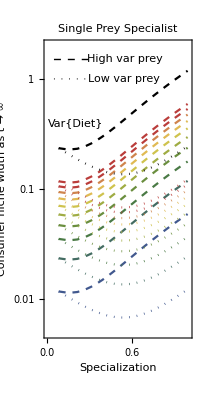
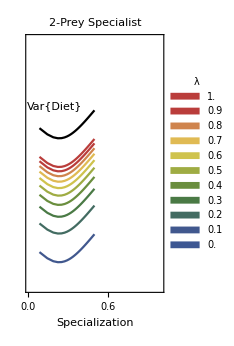
-Graphics--Graphics--Graphics3D-
-Graphics3D-
-Graphics3D-

```mathematica
prey1 = 7;
prey2 = 8;
diff = 0;
VarA = VarTablefunc[{prey1,prey1,diff}];VarZTableA = VarA[[1]];VarXTableA = VarA[[2]];
VarB = VarTablefunc[{prey2,prey2,diff}];VarZTableB = VarB[[1]];VarXTableB = VarB[[2]];
VarAB = VarTablefunc[{prey1,prey2,diff}];VarZTableAB = VarAB[[1]];VarXTableAB = VarAB[[2]];
{"A (Dotted)",EX[[prey1]],VarX[[prey1]]}
{"B (Dashed)",EX[[prey2]],VarX[[prey2]]}

MultipleSpecialistPlotdiff0 = 
Row[{
Show[{

ListLogPlot[VarZTableB,PlotStyle->Directive[{Black,Dashed}],PlotRange->{{0,1},{0.005,2}},Joined->True,AspectRatio->2,FrameLabel->{"Specialization","Consumer niche width as t → ∞"},Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},Epilog->Style[Text["Var{Diet}",{0.2,Log@0.4}],12],PlotLabel->"Single Prey Specialist"],
Table[
ListLogPlot[VarXTableB[[i+1]],PlotRange->All,Frame->True,PlotLabel->"Var{X}",PlotStyle->Directive[Dashed,ColorData["DarkRainbow",i/10]],Joined->True],{i,1,10,1}],

ListLogPlot[VarZTableA,PlotStyle->Directive[{Black,Dotted}],PlotRange->{{0,1},{0.005,2}},Joined->True,Epilog->Style[Text["Var{Z}",{0.15,Log@0.3}],12]],
Table[
ListLogPlot[VarXTableA[[i+1]],PlotRange->All,Frame->True,PlotLabel->"Var{X}",PlotStyle->Directive[Dotted,ColorData["DarkRainbow",i/10]],Joined->True],{i,1,10,1}],

Graphics[{Thick,Dashed,Line[{{0.05,Log@1.5},{0.3,Log@1.5}}]}],
Graphics[{Thick,Dotted,Line[{{0.05,Log@1},{0.3,Log@1}}]}],

Graphics[Text[Style["High var prey"],{0.55,Log@1.5}]],
Graphics[Text["Low var prey",{0.54,Log@1}]]

},ImageSize->200],

Show[{
ListLogPlot[VarZTableAB,Frame->True,PlotStyle->Black,PlotRange->{{0,1},{0.005,2}},Joined->True,AspectRatio->2,FrameLabel->{"Specialization",""},FrameTicks->{{None,None},{Automatic,None}},Epilog->Style[Text["Var{Diet}",{0.2,Log@0.4}],12],PlotLabel->"2-Prey Specialist"],
ListLogPlot[VarXTableAB,PlotRange->All,Frame->True,PlotLabel->"Var{X}",PlotStyle->"DarkRainbow",PlotLegends->SwatchLegend[Table[λ,{λ,0,1,0.1}],LegendLabel->"λ",LegendFunction->(#&),LegendMargins->1,LegendLayout->{"ReversedColumn",1}],Joined->True]
},ImageSize->173],
,"",
Column[{
prey1 = 7;
prey2 = 8;
DparamEx0 =Table[1,{nprey}];
Plot3D[PDF[MarginalDistribution[DirichletDistribution[DparamEx0[[1;;nprey-1]]],{prey1,prey2}],{x,y}],{x,0,1},{y,0,1},PlotRange->All,Mesh->None,Axes->{Automatic,Automatic,None},ColorFunction->"LightTemperatureMap",ImageSize->140],
DparamEx1 =Table[1,{nprey}];
DparamEx1[[prey1]] = 11;
DparamEx1[[prey2]] = 11;
Plot3D[PDF[MarginalDistribution[DirichletDistribution[DparamEx1[[1;;nprey-1]]],{prey1,prey2}],{x,y}],{x,0,1},{y,0,1},PlotRange->All,Mesh->None,Axes->{Automatic,Automatic,None},ColorFunction->"LightTemperatureMap",ImageSize->140],
DparamEx2 =Table[1,{nprey}];
DparamEx2[[prey1]] = 100;
DparamEx2[[prey2]] = 100;
Plot3D[PDF[MarginalDistribution[DirichletDistribution[DparamEx2[[1;;nprey-1]]],{prey1,prey2}],{x,y}],{x,0,1},{y,0,1},PlotRange->All,Mesh->None,Axes->{Automatic,Automatic,None},ColorFunction->"LightTemperatureMap",ImageSize->140]
}]
}," "]
```

```mathematica
ColorData[]
```

{Gradients,Indexed,Named,Physical}

```mathematica
N[11/((1*11) + 11)]
```

0.5

```mathematica
Map[SetOptions[#,Prolog->{{EdgeForm[],Texture[{{{0,0,0,0}}}],Polygon[#,VertexTextureCoordinates->#]&[{{0,0},{1,0},{1,1}}]}}]&,{Graphics3D,ContourPlot3D,ListContourPlot3D,ListPlot3D,Plot3D,ListSurfacePlot3D,ListVectorPlot3D,ParametricPlot3D,RegionPlot3D,RevolutionPlot3D,SphericalPlot3D,VectorPlot3D,BarChart3D}];
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_nichespecialist_diff0.pdf",MultipleSpecialistPlotdiff0]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_nichespecialist_diff0.pdf

{A (Dotted),-7.66,0.25}

{B (Dashed),-7.66,1.21}

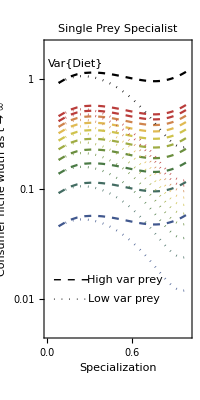
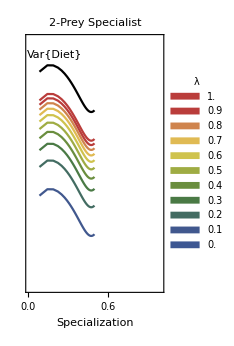

```mathematica
prey1 = 7;
prey2 = 8;
diff = 8;
VarA = VarTablefunc[{prey1,prey1,diff}];VarZTableA = VarA[[1]];VarXTableA = VarA[[2]];
VarB = VarTablefunc[{prey2,prey2,diff}];VarZTableB = VarB[[1]];VarXTableB = VarB[[2]];
VarAB = VarTablefunc[{prey1,prey2,diff}];VarZTableAB = VarAB[[1]];VarXTableAB = VarAB[[2]];
{"A (Dotted)",EX[[prey1]],VarX[[prey1]]}
{"B (Dashed)",EX[[prey2]],VarX[[prey2]]}

MultipleSpecialistPlotdiff8 = 
Row[{
Show[{

ListLogPlot[VarZTableB,PlotStyle->Directive[{Black,Dashed}],PlotRange->{{0,1},{0.005,2}},Joined->True,AspectRatio->2,FrameLabel->{"Specialization","Consumer niche width as t → ∞"},Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},Epilog->Style[Text["Var{Diet}",{0.2,Log@1.4}],12],PlotLabel->"Single Prey Specialist"],
Table[
ListLogPlot[VarXTableB[[i+1]],PlotRange->All,Frame->True,PlotLabel->"Var{X}",PlotStyle->Directive[Dashed,ColorData["DarkRainbow",i/10]],Joined->True],{i,1,10,1}],

ListLogPlot[VarZTableA,PlotStyle->Directive[{Black,Dotted}],PlotRange->{{0,1},{0.005,2}},Joined->True],
Table[
ListLogPlot[VarXTableA[[i+1]],PlotRange->All,Frame->True,PlotLabel->"Var{X}",PlotStyle->Directive[Dotted,ColorData["DarkRainbow",i/10]],Joined->True],{i,1,10,1}],

Graphics[{Thick,Dashed,Line[{{0.05,Log@.015},{0.3,Log@.015}}]}],
Graphics[{Thick,Dotted,Line[{{0.05,Log@.01},{0.3,Log@.01}}]}],

Graphics[Text[Style["High var prey"],{0.55,Log@.015}]],
Graphics[Text["Low var prey",{0.54,Log@.01}]]

},ImageSize->200],

Show[{
ListLogPlot[VarZTableAB,Frame->True,PlotStyle->Black,PlotRange->{{0,1},{0.005,2}},Joined->True,AspectRatio->2,FrameLabel->{"Specialization",""},FrameTicks->{{None,None},{Automatic,None}},Epilog->Style[Text["Var{Diet}",{0.2,Log@1.4}],12],PlotLabel->"2-Prey Specialist"],
ListLogPlot[VarXTableAB,PlotRange->All,Frame->True,PlotLabel->"Var{X}",PlotStyle->"DarkRainbow",PlotLegends->SwatchLegend[Table[λ,{λ,0,1,0.1}],LegendLabel->"λ",LegendFunction->(#&),LegendMargins->1,LegendLayout->{"ReversedColumn",1}],Joined->True]
},ImageSize->173]
}]
```

```mathematica
Mean[{-15.5,-17.5,-15.6,-15.5,-14.3,-15.4,-15.659999999999997,-15.659999999999997,-15.8,-13.3,-17.5,-16.2}]
```

-15.66

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_nichespecialist.pdf",MultipleSpecialistPlot]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_nichespecialist.pdf

Variance as a function of the dispersion parameter

```mathematica
VarZGamma = Table[
nprey = 12;
EX = {-15.5,-17.5,-15.6,-15.5,-14.3,-15.4,-16.0,-17.0,-15.8,-13.3,-17.5,-16.2};
VarX = {1.00,0.81,0.49,0.81,0.81,0.81,0.25,1.21,0.64,1.21,1.96,1.00};
timebetweenencounters =Table[5,{nprey}];
Dparam = Table[v/timebetweenencounters[[i]],{i,1,12}];
a0 = Total[Dparam];
Ep = N[Dparam/a0];
Varp = N[Table[(Dparam[[i]]*(a0-Dparam[[i]]))/(a0^2*(a0+1)),{i,1,nprey}]];
Covp = N[Table[(-Dparam[[i]]*Dparam[[j]])/(a0^2*(a0+1))Boole[i ≠ j],{i,1,nprey},{j,1,nprey}]];
VarZ = N[Sum[Varp[[i]]*VarX[[i]] + Ep[[i]]^2*VarX[[i]] + EX[[i]]^2*Varp[[i]] + Sum[Covp[[i]][[j]]*EX[[i]]*EX[[j]]Boole[i ≠ j],{j,1,nprey}],{i,1,nprey}]];
VarDiet = (1-Sum[Ep[[i]]^2, {i,1,nprey}])/(nprey*(a0 + 1));
{VarDiet,VarZ},
{v,0.01,1000,0.1}];
VarXGamma = Table[{VarZGamma[[i]][[1]],(λ*VarZGamma[[i]][[2]])/2},{λ,0,1,0.1},{i,1,Length[VarZGamma]}];
```

```mathematica
Total[Ep]
```

1.

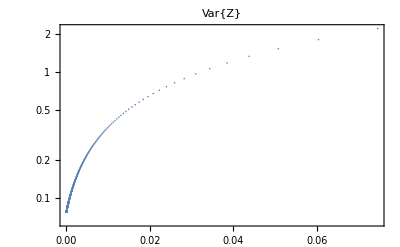

```mathematica
ListLogPlot[VarZGamma,PlotRange->All,Frame->True,PlotLabel->"Var{Z}"]
```

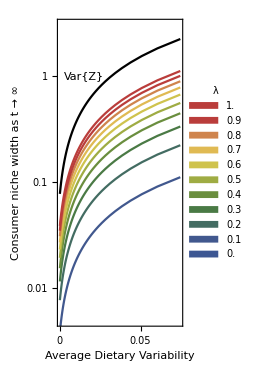

```mathematica
VarSpatialPlot = Show[{
ListLogPlot[VarZGamma,Frame->True,PlotStyle->Black,PlotRange->{All,{0.005,3}},Joined->True,AspectRatio->2,FrameLabel->{"Average Dietary Variability","Consumer niche width as t → ∞"},Epilog->Style[Text["Var{Z}",{0.015,Log@1}],12],FrameTicks->{{All,None},{{0,0.01,0.03,0.05,0.07},None}}],
ListLogPlot[VarXGamma,PlotRange->All,Frame->True,PlotLabel->"Var{X}",PlotStyle->"DarkRainbow",PlotLegends->SwatchLegend[Table[λ,{λ,0,1,0.1}],LegendLabel->"λ",LegendFunction->(#&),LegendMargins->1,LegendLayout->{"ReversedColumn",1}],Joined->True]
},ImageSize->193]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_nichegamma.pdf",VarSpatialPlot]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_nichegamma.pdf

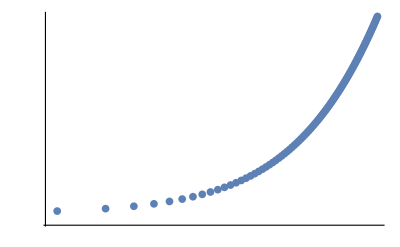

```mathematica
ListLogLogPlot[VarZGamma,Ticks->None]
```

```mathematica
VarXTable3D = Table[{λ,Log[VarZTable[[i]][[1]]],(λ*VarZTable[[i]][[2]])/2},{λ,0,1,0.1},{i,1,Length[VarZTable]}];
```

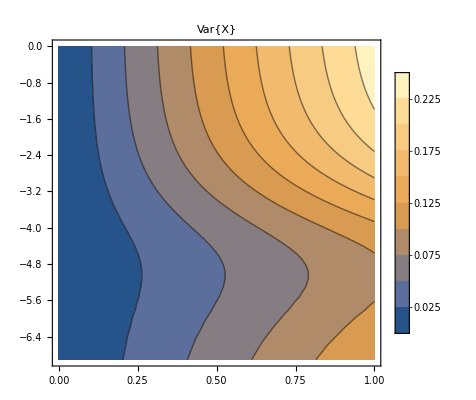

```mathematica
ListContourPlot[Flatten[VarXTable3D,1],PlotRange->All,Frame->True,PlotLabel->"Var{X}",PlotLegends->True]
```

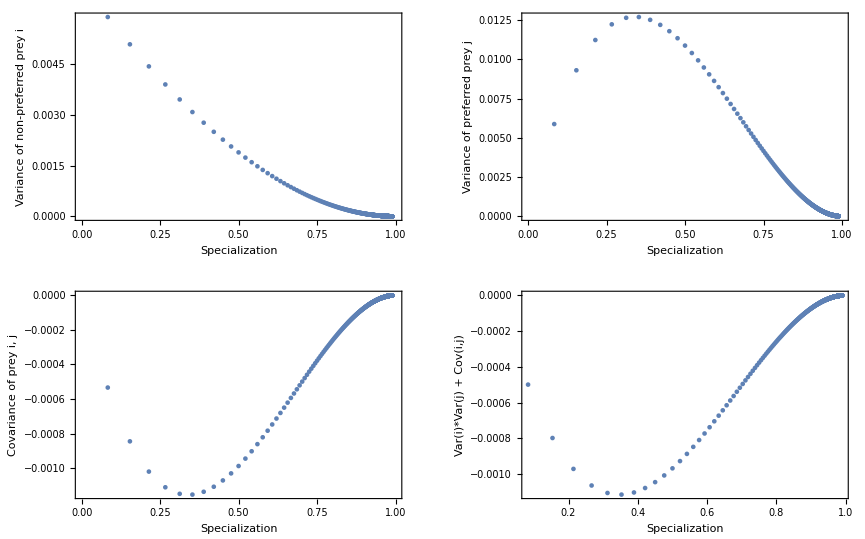

```mathematica
nprey=12;
prey1 = 7;
prey2=7;
VarianceElements=GraphicsGrid[{
{
ListPlot[

VarVector6=Table[
Dparam =Table[1,{nprey}];
Dparam[[prey1]] = a;
Dparam[[prey2]] = a;
a0 = Total[Dparam];
VarVector=N[Table[(Dparam[[i]]*(a0-Dparam[[i]]))/(a0^2*(a0+1)),{i,1,nprey}]];
{a/a0,VarVector[[6]]},
{a,1,1000,1}],PlotRange->{{0,1},All},ImageSize->400,Frame->True,FrameLabel->{"Specialization","Variance of non-preferred prey i"}],
ListPlot[
VarVector7=Table[
Dparam =Table[1,{nprey}];
Dparam[[prey1]] = a;
Dparam[[prey2]] = a;
a0 = Total[Dparam];
VarVector=N[Table[(Dparam[[i]]*(a0-Dparam[[i]]))/(a0^2*(a0+1)),{i,1,nprey}]];
{a/a0,VarVector[[7]]},
{a,1,1000,1}],PlotRange->{{0,1},All},ImageSize->400,Frame->True,FrameLabel->{"Specialization","Variance of preferred prey j"}]},
{
ListPlot[
COV=Table[
Dparam =Table[1,{nprey}];
Dparam[[prey1]] = a;
Dparam[[prey2]] = a;
a0 = Total[Dparam];
COVVector=N[Table[(-Dparam[[i]]*Dparam[[j]])/(a0^2*(a0+1))Boole[i ≠ j],{i,1,nprey},{j,1,nprey}]];
{a/a0,COVVector[[6,7]]},
{a,1,1000,1}],PlotRange->{{0,1},All},ImageSize->400,Frame->True,FrameLabel->{"Specialization","Covariance of prey i, j"}],
ListPlot[Transpose[{VarVector6[[All,1]],VarVector6[[All,2]] * VarVector7[[All,2]] + COV[[All,2]]}],PlotRange->All,Frame->True,FrameLabel->{"Specialization","Var(i)*Var(j) + Cov(i,j)"}]}
}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_varianceelements.pdf",VarianceElements]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_varianceelements.pdf